# PS 14 — Rania 3.28.2025

## 35

```mathematica
(*35.1 Use Interpreter to find the location of the Eiffel Tower.*)
Interpreter["Location"]["Eiffel Tower"]
```

GeoPosition[{48.8583,2.29444}]

```mathematica
(*35.2 Use Interpreter to find a university referred to as “U of T”.*)
Interpreter["University"]["U of T"]
```

University of Toronto

```mathematica
(*35.3 Use Interpreter to find the chemicals referred to as C2H4,C2H6 and C3H8.*)
Interpreter["Chemical"][{"C2H4", "C2H6", "C3H8"}]
```

{ethylene,ethane,propane}

```mathematica
(*35.4 Use Interpreter to interpret the date “20140108”.*)
```

```mathematica
Interpreter["Date"]["20140108"]
```

Wed 8 Jan 2014

```mathematica
(*35.5 Find universities that can be referred to as “U of X”,where X is any letter of the alphabet*)
DeleteCases[Interpreter["University"][StringJoin["U of ",#]&/@ ToUpperCase[Alphabet[]]],_Failure]
(*did research on DeleteCases vs DeleteMissing*)
```

{University of Birjand,University of California-Berkeley,The University of Edinburgh,University of Georgia,University of Houston,University of Illinois at Urbana-Champaign,University of Lethbridge,University of Michigan-Ann Arbor,University of Phoenix-Online Campus,University of Regina,University of Saskatchewan,University of Toronto}

```mathematica
(*35.6Find which US state capital names can be interpreted as movie titles - use CommonName to get the string versions of entity names*)
DeleteCases[Interpreter["Movie"]/@CommonName/@ EntityClass["AdministrativeDivision","AllUSStatesPlusDC"][EntityProperty["AdministrativeDivision","CapitalCity"]],_Failure]
```

{Phoenix,Honolulu,Topeka,Annapolis,Lincoln,Santa Fe,Expedition: Bismarck,Columbus,Providence,Nashville,Olympia,Madison,Cheyenne}

```mathematica
(*35.7 Find cities that can be referred to by permutations of the letters a,i,l and m.*)
```

```mathematica
DeleteCases[Interpreter["City"]/@StringJoin/@Permutations[{"a","i","l","m"}],_Failure]
```

{Alim,Amli,Balm,Ilam,Lami,Lima,Lamai,Mali,Milah,Mali}

```mathematica
(*35.8 Make a word cloud of country names in the Wikipedia article on “gunpowder”.*)
```

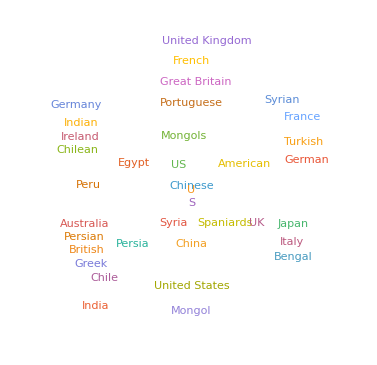

```mathematica
WordCloud[TextCases[WikipediaData["gunpowder"],"Country"]]
(*not sure why it failed when it worked in the chapter*)
```

```mathematica
(*35.9 Find all nouns in “She sells seashells by the sea shore.”*)
```

```mathematica
TextCases["She sells seashells by the sea shore","Noun"]
```

{seashells,sea,shore}

```mathematica
(*35.10 Use TextCases to find the number of nouns,verbs and adjectives in the first 1000 characters of the Wikipedia article on computers.*)
```

```mathematica
Length[TextCases[StringJoin[Characters[WikipediaData["computers"]][[1;;1000]]],#]]&/@{"Noun","Verb", "Adjective"}
```

{54,23,20}

```mathematica
(*35.11 Find the grammatical structure of the first sentence of the Wikipedia article about computers.*)
```

```mathematica
TextStructure[TextSentences[WikipediaData["computers"]][[1]]]
```

A
Determinercomputer
Noun
Noun Phrase  is
Verb    a
Determinermachine
Noun
Noun Phrase    that
Wh-Determiner
Wh-Noun Phrase  can
Verb  be
Verb  programmed
Verb    to
Preposition    automatically
Adverb
Adverb Phrasecarry
Verb  out
Particle
Particle    sequences
Noun
Noun Phrase  of
Preposition      arithmetic
Adjectiveor
Conjunctionlogical
Adjective
Adjective Phraseoperations
Noun
Noun Phrase  (
Punctuation  computation
Noun
Noun Phrase)
Punctuation
Parenthetical
Noun Phrase
Prepositional Phrase
Noun Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Noun Phrase
Verb Phrase.
Punctuation
Sentence

```mathematica
(*35.12Find the 10 most common nouns in ExampleData[{"Text","AliceInWonderland"}]*)
Reverse[Sort[Counts[TextCases[ExampleData[{"Text","AliceInWonderland"}],"Noun"]]]][[1;;10]] //Keys
```

{Rabbit,door,voice,time,Mouse,way,moment,thing,head,garden}

```mathematica
(*35.13 Make a community graph plot of the graph representation of the text structure of the first sentence of the Wikipedia article about language.*)
CommunityGraphPlot[TextStructure[TextSentences[WikipediaData["language"]],"DependencyGraphs"][[1]]]
(*so confused why the CommunityGraphPlot is not working*)
```

CommunityGraphPlot::graph: A graph object is expected at position 1 in ….

CommunityGraphPlot[{-Graphics-}]

```mathematica
(*35.14 Make a list of numbers of nouns,verbs,adjectives and adverbs found by WordList in English.*)
```

```mathematica
Length[WordList[#]]&/@{"Noun","Verb","Adjective","Adverb"}
```

{24493,6503,11392,3120}

## 36

```mathematica
(*36.1 Create a website that displays a new random number up to 1000 at size 100 every time it is visited.*)
CloudPublish[Delayed[Style[RandomInteger[1000],1000]]]
```

CloudObject[https://www.wolframcloud.com/obj/b066fbbc-8332-44d5-ab66-352698a073e3]

```mathematica
(*36.2 Publish a form on the web that takes a number x and returns x^x *)CloudPublish[FormFunction[{"x"->"Number"},#x^#x&]]
```

CloudObject[https://www.wolframcloud.com/obj/a1e72ad6-3270-4982-8ee8-42d672016b73]

```mathematica
(*36.3 Publish a form on the web that takes numbers x and y and computes x^y*)
CloudPublish[FormFunction[{"x"->"Number","y"->"Number"},#x^#y&]]
```

CloudObject[https://www.wolframcloud.com/obj/285c2ddf-0ef0-4ce9-8e98-9aa6c8d08eea]

```mathematica
(*36.4 Publish a form on the web that takes the topic of a Wikipedia page and gives a word cloud for the page*)CloudPublish[FormFunction[{"topic"->"String"},WordCloud[WikipediaData[#topic]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/a1c93239-9f04-41c0-8b5d-df998e85d1cc]

```mathematica
(*36.5 Publish a form page on the web that takes a string and repeatedly gives a reversed version at size 50*)CloudPublish[FormFunction[{"String"->"String"},Style[StringReverse[#String],50]&]]
```

CloudObject[https://www.wolframcloud.com/obj/06f5f8b0-4c96-45c7-a133-185a1b7e7e72]

```mathematica
(*36.6 Publish a form page on the web that takes an integer n and repeatedly generates a picture of a polygon with a random color and n sides*)CloudPublish[FormPage[{"n"->"Integer"},Graphics[{RandomColor[],RegularPolygon[#n]}]&]]
```

CloudObject[https://www.wolframcloud.com/obj/71484956-6bfa-4fa5-bb0e-3d6fa31cf6ed]

```mathematica
(*36.7 Publish a form page that takes a location and a number n and repeatedly gives a map of the n nearest volcanoes to the location*)CloudPublish[FormPage[{"location"->"Location","n"->"Number"},GeoListPlot[Nearest[EntityList["Volcano"],#location,#n]]&]]
```

CloudObject[https://www.wolframcloud.com/obj/03e1f956-1c01-413b-b2a8-0dcbf9de4812]